# H3 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## The exact solution

```mathematica
(* molecule distances *)
moldists=DeleteDuplicates@Flatten@{Range[0.45,1.5,0.05],Range[1.5,2.5,0.1],Range[2.5,6,0.25]}
```

{0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.}

```mathematica
Length/@{Range[0.45,1.5,0.05],Range[1.5,2.5,0.1],Range[2.5,6,0.25]}
```

{22,11,15}

```mathematica
(* ground states of H3 *)
gsH3=Table[
	fname=ToString@StringForm["H3_hamiltonians/H3_``.txt", NumberForm[dist, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 <|
"distance"->dist,
"hamfile"->fname,
"hamiltonian"->ham,
"groundstate"->Min@Eigenvalues@CalcPauliStringMatrix@ham
|>
,{dist,moldists}];
```

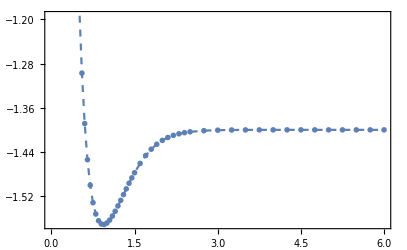

```mathematica
ListPlot[gsH3[[All,{"distance","groundstate"}]],PlotMarkers->{"OpenMarkers",6},PlotStyle->Dashed,Joined->True,Frame->True]
```

## VQE on the virtual device using random ansatz methode

### (0) Original noisy setting: H3onSQC0.mx

Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H3onSQC0, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H3onSQC0.mx", H3onSQC0];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH3}]

Compilation with automatically generated ansatz at Mon 20 Feb 2023 19:54:52 with grad NGAN

@cycle1:Mon 20 Feb 2023 19:59:04, fev:767, <E>: -0.30900539365370727 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 0, 14}

@cycle2:Mon 20 Feb 2023 20:05:25, fev:1644, <E>: -0.5891909661761223 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 24, 34}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:08:29, fev:2161, <E>: -0.5891909661761223 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 24, 51}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 20:12:53, fev:2791, <E>: -0.5891909661761223 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 24, 81}

dist 0.45 ; runtime 18.0551 min ; ϵ=0.405815

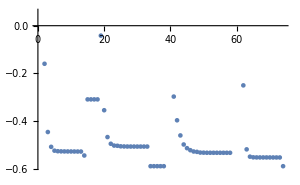

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:12:55 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:18:39, fev:1057, <E>: -0.7626061625759073 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 5, 24}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:24:07, fev:1583, <E>: -0.7626061625759073 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 5, 43}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:32:58, fev:2287, <E>: -0.7626061625759073 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 5, 67}

dist 0.5 ; runtime 20.6955 min ; ϵ=0.407926

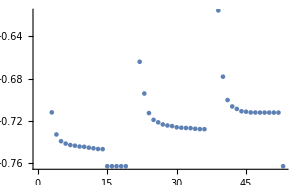

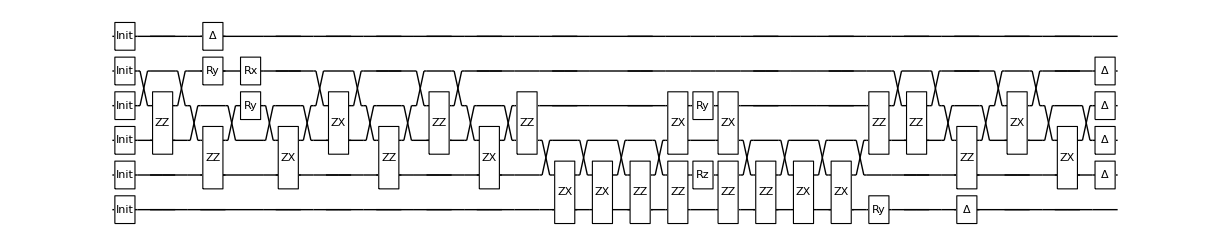

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:33:37 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:39:32, fev:1282, <E>: -0.947634664484579 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 9, 25}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:44:15, fev:1846, <E>: -0.947634664484579 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 9, 43}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:51:31, fev:2545, <E>: -0.947634664484579 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 9, 58}

dist 0.55 ; runtime 18.2422 min ; ϵ=0.349363

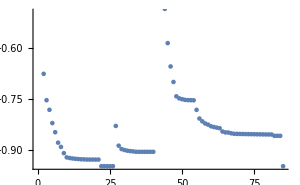

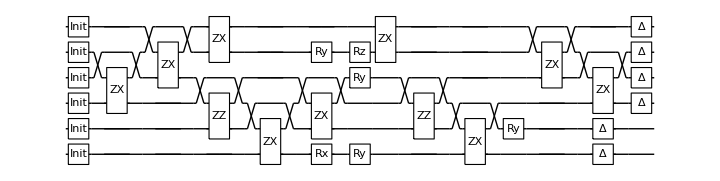

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:51:52 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:57:44, fev:1024, <E>: -1.0545642512633324 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 3, 24}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 21:04:42, fev:1609, <E>: -1.0545642512633324 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 3, 43}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 21:13:56, fev:2311, <E>: -1.0545642512633324 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 3, 72}

dist 0.6 ; runtime 24.912 min ; ϵ=0.333751

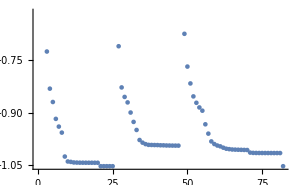

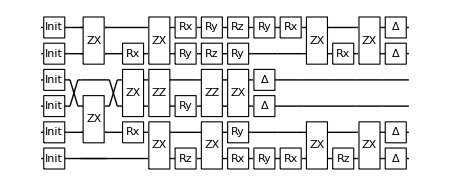

Compilation with automatically generated ansatz at Mon 20 Feb 2023 21:16:47 with grad NGAN

@cycle1:Mon 20 Feb 2023 21:21:11, fev:854, <E>: -1.1573955067457617 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 17, 24}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 21:25:30, fev:1413, <E>: -1.1573955067457617 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 17, 44}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 21:31:29, fev:2101, <E>: -1.1573955067457617 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 17, 78}

dist 0.65 ; runtime 14.788 min ; ϵ=0.296393

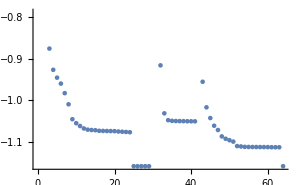

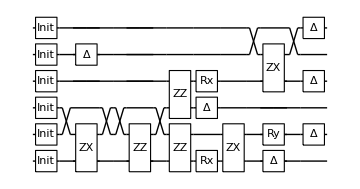

Compilation with automatically generated ansatz at Mon 20 Feb 2023 21:31:34 with grad NGAN

@cycle1:Mon 20 Feb 2023 21:35:21, fev:698, <E>: -1.2225727809807796 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 5, 1, 11, 35}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 21:39:15, fev:1226, <E>: -1.2225727809807796 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 5, 1, 11, 62}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 21:44:37, fev:1870, <E>: -1.2225727809807796 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 5, 1, 11, 108}

dist 0.7 ; runtime 13.0733 min ; ϵ=0.277364

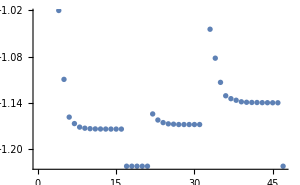

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 21:44:39 with grad NGAN

@cycle1:Mon 20 Feb 2023 21:49:23, fev:798, <E>: -1.2036312745318904 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 0, 32}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 21:55:00, fev:1324, <E>: -1.2036312745318904 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 0, 52}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:04:04, fev:2062, <E>: -1.2036312745318904 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 0, 89}

dist 0.75 ; runtime 19.9913 min ; ϵ=0.268183

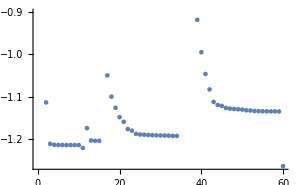

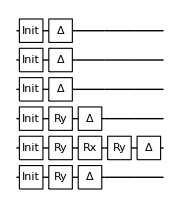

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:04:38 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:08:52, fev:752, <E>: -1.1043684741496682 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 4, 26}

@cycle2:Mon 20 Feb 2023 22:14:22, fev:1509, <E>: -1.2867448753226016 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 27, 39}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:17:40, fev:1981, <E>: -1.2867448753226016 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 27, 48}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 22:22:31, fev:2606, <E>: -1.2867448753226016 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 27, 62}

dist 0.8 ; runtime 17.873 min ; ϵ=0.265284

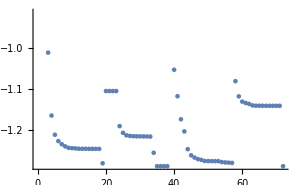

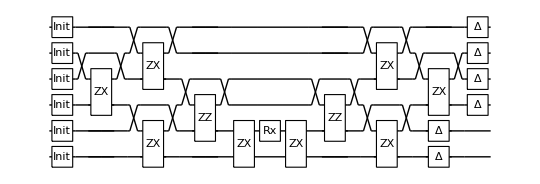

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:22:31 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:26:39, fev:787, <E>: -1.3041748098529735 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 7, 26}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 22:31:16, fev:1300, <E>: -1.3041748098529735 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 7, 49}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:37:53, fev:1903, <E>: -1.3041748098529735 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 7, 69}

dist 0.85 ; runtime 15.4973 min ; ϵ=0.260004

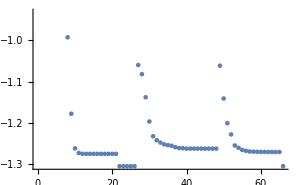

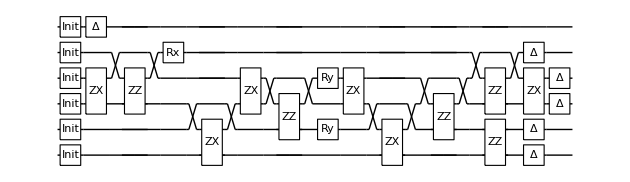

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:38:01 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:41:35, fev:646, <E>: -1.0111597470202343 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 0, 29}

@cycle2:Mon 20 Feb 2023 22:46:09, fev:1478, <E>: -1.3036060321618843 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 14, 54}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:49:16, fev:1963, <E>: -1.3036060321618843 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 14, 69}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 22:53:29, fev:2574, <E>: -1.3036060321618843 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 14, 80}

dist 0.9 ; runtime 15.5114 min ; ϵ=0.266374

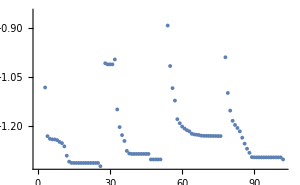

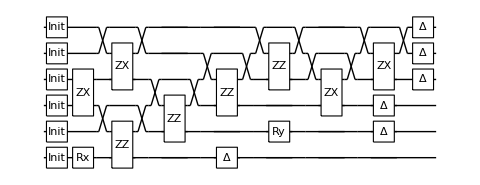

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:53:32 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:58:44, fev:980, <E>: -1.3212898549853436 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 17}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:03:55, fev:1541, <E>: -1.3212898549853436 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 31}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:11:06, fev:2205, <E>: -1.3212898549853436 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 51}

dist 0.95 ; runtime 17.972 min ; ϵ=0.249685

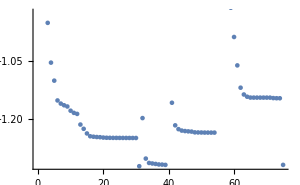

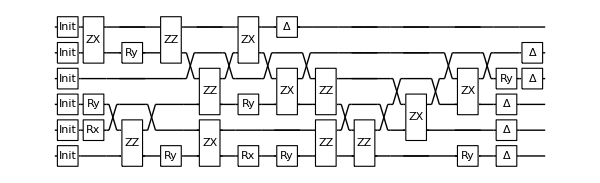

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:11:30 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:15:49, fev:806, <E>: -0.8191880650834236 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 9, 26}

@cycle2:Mon 20 Feb 2023 23:22:09, fev:1849, <E>: -1.3129276690123342 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 34, 49}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:25:31, fev:2364, <E>: -1.3129276690123342 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 34, 54}

@cycle4:Mon 20 Feb 2023 23:31:09, fev:3351, <E>: -1.3499406797106612 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 54, 68}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 23:34:21, fev:3915, <E>: -1.3499406797106612 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 54, 87}

Slowing down @cycle 6

@cycle6:Mon 20 Feb 2023 23:39:06, fev:4626, <E>: -1.3499406797106612 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 54, 111}

dist 1. ; runtime 27.6208 min ; ϵ=0.218411

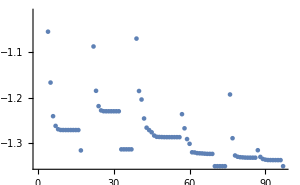

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:39:08 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:44:08, fev:947, <E>: -0.8479493577971394 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 23, 15}

@cycle2:Mon 20 Feb 2023 23:48:46, fev:1737, <E>: -0.7665686851482826 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 29, 0, 29, 39}

@cycle3:Mon 20 Feb 2023 23:54:20, fev:2568, <E>: -1.1936780060059258 nansatz: 30 merged-smallθ-metric-bf-gmerged: {1, 48, 0, 29, 60}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 23:59:00, fev:3066, <E>: -1.1936780060059258 nansatz: 30 merged-smallθ-metric-bf-gmerged: {1, 48, 0, 29, 74}

@cycle5:Tue 21 Feb 2023 00:08:16, fev:4234, <E>: -1.154437760853616 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 51, 92}

@cycle6:Tue 21 Feb 2023 00:17:28, fev:5620, <E>: -1.054130351606989 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 76, 1, 89, 102}

@cycle7:Tue 21 Feb 2023 00:23:21, fev:6605, <E>: -1.2918702264318362 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 94, 1, 95, 124}

Slowing down @cycle 8

@cycle8:Tue 21 Feb 2023 00:28:02, fev:7219, <E>: -1.2918702264318362 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 94, 1, 95, 148}

Slowing down @cycle 9

@cycle9:Tue 21 Feb 2023 00:34:31, fev:7990, <E>: -1.2918702264318362 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 94, 1, 95, 170}

dist 1.05 ; runtime 55.6722 min ; ϵ=0.27116

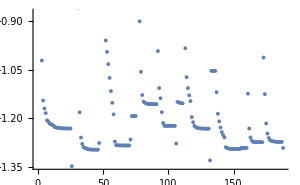

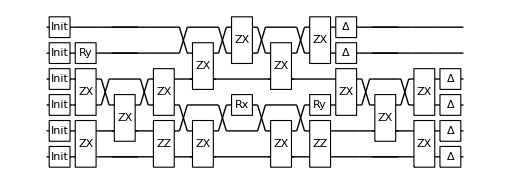

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:34:48 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:38:54, fev:694, <E>: -1.3437210414999958 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 14, 29}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 00:43:07, fev:1208, <E>: -1.3437210414999958 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 14, 53}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 00:48:16, fev:1821, <E>: -1.3437210414999958 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 14, 84}

dist 1.1 ; runtime 13.489 min ; ϵ=0.212016

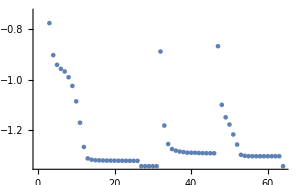

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:48:18 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:53:45, fev:1085, <E>: -1.3178310507931306 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 10, 20}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 00:59:08, fev:1629, <E>: -1.3178310507931306 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 10, 35}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:06:09, fev:2270, <E>: -1.3178310507931306 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 10, 56}

dist 1.15 ; runtime 18.7127 min ; ϵ=0.22922

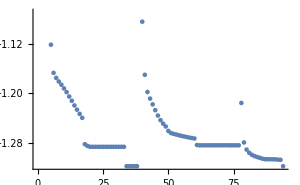

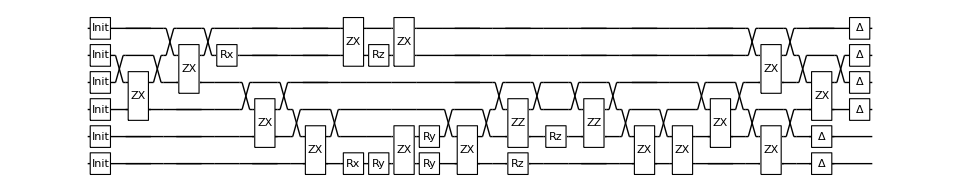

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:07:01 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:11:25, fev:783, <E>: -1.0041690304093545 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 28, 36}

@cycle2:Tue 21 Feb 2023 01:16:23, fev:1632, <E>: -1.3309511469750193 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 50, 60}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:18:45, fev:2071, <E>: -1.3309511469750193 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 50, 79}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 01:22:18, fev:2639, <E>: -1.3309511469750193 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 50, 99}

dist 1.2 ; runtime 15.3158 min ; ϵ=0.206489

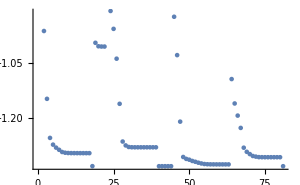

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:22:20 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:25:58, fev:658, <E>: -0.32135079410588885 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 12, 41}

@cycle2:Tue 21 Feb 2023 01:30:35, fev:1386, <E>: -1.3212237965591924 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 29, 0, 30, 58}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:32:50, fev:1814, <E>: -1.3212237965591924 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 29, 0, 30, 77}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 01:36:12, fev:2395, <E>: -1.3212237965591924 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 29, 0, 30, 95}

dist 1.25 ; runtime 13.8888 min ; ϵ=0.20606

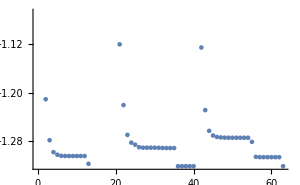

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:36:13 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:41:40, fev:1052, <E>: -1.2950419295915632 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 24}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:47:13, fev:1572, <E>: -1.2950419295915632 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 47}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:54:54, fev:2205, <E>: -1.2950419295915632 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 70}

dist 1.3 ; runtime 19.3935 min ; ϵ=0.221851

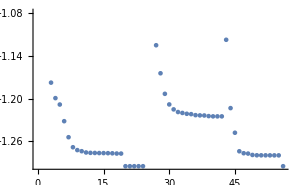

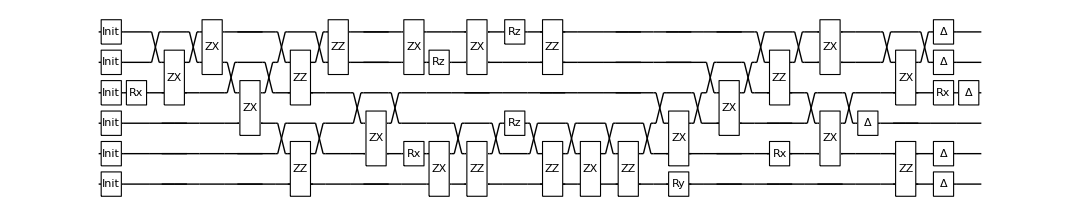

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:55:37 with grad NGAN

@cycle1:Tue 21 Feb 2023 02:01:23, fev:1025, <E>: -1.1749381231018703 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 0, 27}

@cycle2:Tue 21 Feb 2023 02:08:15, fev:1886, <E>: -0.9627652951661124 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 24, 39}

@cycle3:Tue 21 Feb 2023 02:16:29, fev:2909, <E>: -1.0418884034882818 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 46, 0, 38, 73}

@cycle4:Tue 21 Feb 2023 02:24:21, fev:3759, <E>: -1.1836646909552888 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 73, 0, 46, 96}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 02:30:04, fev:4260, <E>: -1.1836646909552888 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 73, 0, 46, 112}

Slowing down @cycle 6

@cycle6:Tue 21 Feb 2023 02:38:17, fev:4897, <E>: -1.1836646909552888 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 73, 0, 46, 125}

dist 1.35 ; runtime 42.6818 min ; ϵ=0.322852

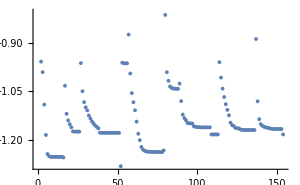

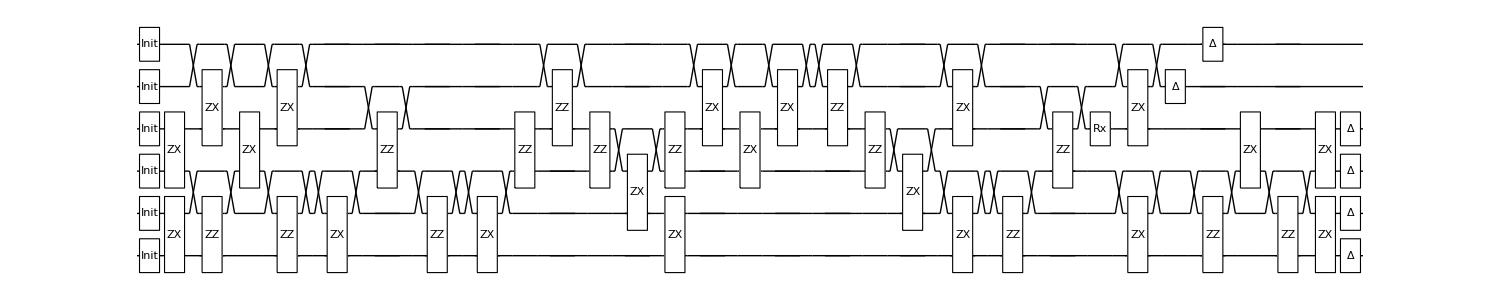

Compilation with automatically generated ansatz at Tue 21 Feb 2023 02:38:18 with grad NGAN

@cycle1:Tue 21 Feb 2023 02:42:50, fev:878, <E>: -1.2841337872245866 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 10, 30}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 02:47:06, fev:1406, <E>: -1.2841337872245866 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 10, 53}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 02:53:38, fev:2023, <E>: -1.2841337872245866 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 10, 82}

dist 1.4 ; runtime 15.707 min ; ϵ=0.212222

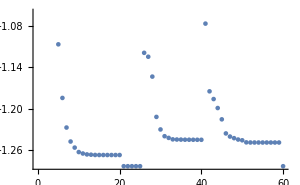

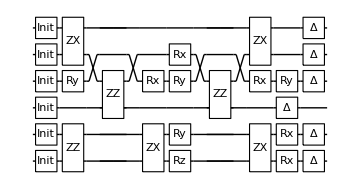

Compilation with automatically generated ansatz at Tue 21 Feb 2023 02:54:01 with grad NGAN

@cycle1:Tue 21 Feb 2023 03:00:31, fev:1090, <E>: -1.1247401298475015 nansatz: 41 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 0, 15}

@cycle2:Tue 21 Feb 2023 03:12:48, fev:2627, <E>: -0.8576311757788357 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 31, 31}

@cycle3:Tue 21 Feb 2023 03:30:39, fev:4518, <E>: -1.2714785415435474 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 87, 59}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 03:33:23, fev:4982, <E>: -1.2714785415435474 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 87, 87}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 03:37:20, fev:5573, <E>: -1.2714785415435474 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 87, 103}

dist 1.45 ; runtime 43.3413 min ; ϵ=0.215089

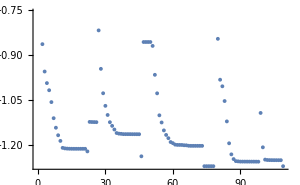

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 03:37:21 with grad NGAN

@cycle1:Tue 21 Feb 2023 03:41:39, fev:822, <E>: -0.9411063352884596 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 19, 38}

@cycle2:Tue 21 Feb 2023 03:47:35, fev:1725, <E>: -0.8520790111031749 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 45, 60}

@cycle3:Tue 21 Feb 2023 03:53:19, fev:2658, <E>: -1.2500451213114585 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 81, 77}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 03:56:01, fev:3106, <E>: -1.2500451213114585 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 81, 88}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 03:59:44, fev:3685, <E>: -1.2500451213114585 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 81, 105}

dist 1.5 ; runtime 22.4273 min ; ϵ=0.227227

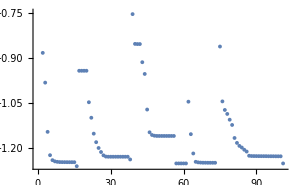

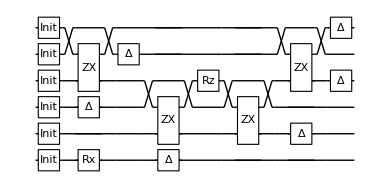

Compilation with automatically generated ansatz at Tue 21 Feb 2023 03:59:47 with grad NGAN

@cycle1:Tue 21 Feb 2023 04:05:11, fev:934, <E>: -1.0542180732227215 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 0, 27}

@cycle2:Tue 21 Feb 2023 04:12:08, fev:1709, <E>: -0.9219497630643779 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 36, 0, 15, 54}

@cycle3:Tue 21 Feb 2023 04:17:35, fev:2563, <E>: -1.047767803216283 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 57, 0, 33, 96}

@cycle4:Tue 21 Feb 2023 04:23:09, fev:3355, <E>: -0.9679504972970541 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 76, 0, 51, 113}

@cycle5:Tue 21 Feb 2023 04:28:23, fev:4136, <E>: -1.217784849083744 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 67, 136}

@cycle6:Tue 21 Feb 2023 04:32:32, fev:4938, <E>: -0.9772133741374713 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 105, 0, 82, 156}

@cycle7:Tue 21 Feb 2023 04:39:02, fev:5988, <E>: -1.1930902130096392 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 128, 0, 96, 184}

Slowing down @cycle 8

@cycle8:Tue 21 Feb 2023 04:42:37, fev:6464, <E>: -1.1930902130096392 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 128, 0, 96, 194}

Slowing down @cycle 9

@cycle9:Tue 21 Feb 2023 04:48:04, fev:7094, <E>: -1.1930902130096392 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 128, 0, 96, 215}

dist 1.6 ; runtime 48.394 min ; ϵ=0.267378

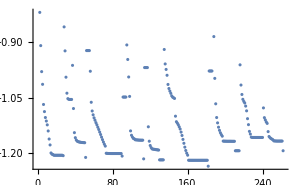

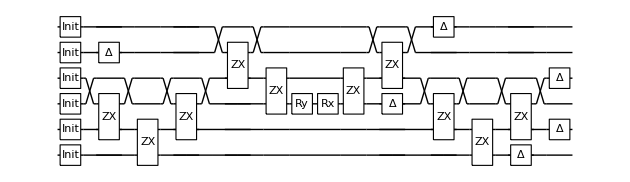

Compilation with automatically generated ansatz at Tue 21 Feb 2023 04:48:11 with grad NGAN

@cycle1:Tue 21 Feb 2023 04:52:24, fev:855, <E>: -1.2308341509149126 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 14, 35}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 04:56:46, fev:1372, <E>: -1.2308341509149126 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 14, 59}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 05:02:31, fev:1955, <E>: -1.2308341509149126 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 14, 84}

dist 1.7 ; runtime 14.6327 min ; ϵ=0.215473

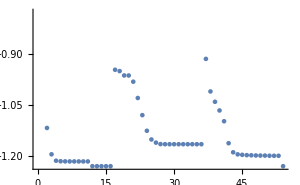

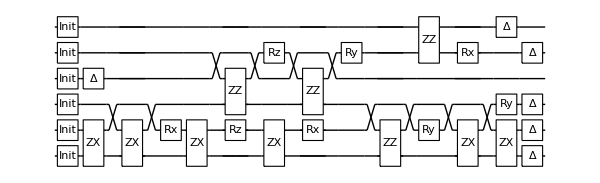

Compilation with automatically generated ansatz at Tue 21 Feb 2023 05:02:49 with grad NGAN

@cycle1:Tue 21 Feb 2023 05:06:37, fev:808, <E>: -1.2331706611948259 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 10, 15}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 05:10:33, fev:1282, <E>: -1.2331706611948259 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 10, 31}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 05:16:24, fev:1887, <E>: -1.2331706611948259 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 10, 46}

dist 1.8 ; runtime 13.8069 min ; ϵ=0.201632

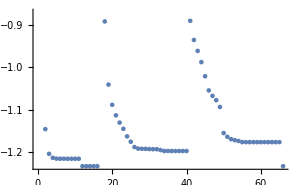

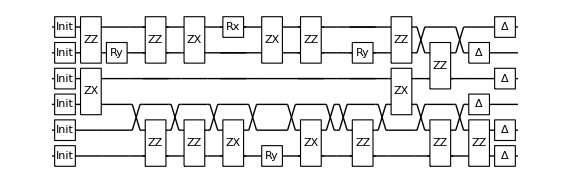

Compilation with automatically generated ansatz at Tue 21 Feb 2023 05:16:37 with grad NGAN

@cycle1:Tue 21 Feb 2023 05:20:30, fev:804, <E>: -1.252298621500021 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 9, 36}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 05:24:18, fev:1284, <E>: -1.252298621500021 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 9, 51}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 05:30:35, fev:1890, <E>: -1.252298621500021 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 9, 80}

dist 1.9 ; runtime 14.1153 min ; ϵ=0.173443

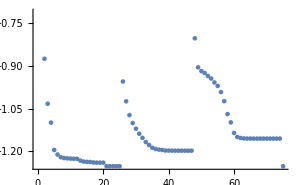

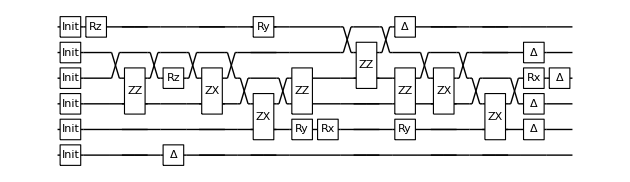

Compilation with automatically generated ansatz at Tue 21 Feb 2023 05:30:45 with grad NGAN

@cycle1:Tue 21 Feb 2023 05:35:25, fev:884, <E>: -1.229745875532393 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 11, 0, 6, 31}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 05:38:58, fev:1315, <E>: -1.229745875532393 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 11, 0, 6, 50}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 05:45:01, fev:1929, <E>: -1.229745875532393 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 11, 0, 6, 61}

dist 2. ; runtime 14.4853 min ; ϵ=0.189041

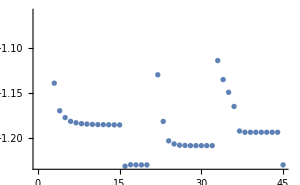

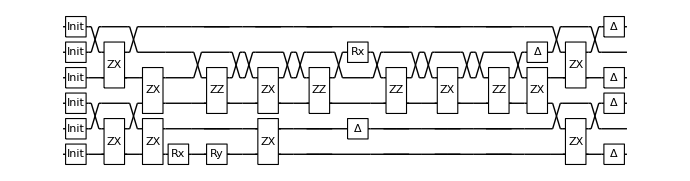

Compilation with automatically generated ansatz at Tue 21 Feb 2023 05:45:14 with grad NGAN

@cycle1:Tue 21 Feb 2023 05:50:12, fev:1029, <E>: -0.8253930996888602 nansatz: 22 merged-smallθ-metric-bf-gmerged: {2, 1, 0, 0, 33}

@cycle2:Tue 21 Feb 2023 05:56:42, fev:2072, <E>: -0.8223826271893253 nansatz: 27 merged-smallθ-metric-bf-gmerged: {2, 28, 0, 0, 63}

@cycle3:Tue 21 Feb 2023 06:03:05, fev:3032, <E>: -1.0968198013767299 nansatz: 43 merged-smallθ-metric-bf-gmerged: {2, 52, 0, 0, 90}

@cycle4:Tue 21 Feb 2023 06:08:46, fev:3891, <E>: -0.9844500713700879 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 64, 0, 46, 96}

@cycle5:Tue 21 Feb 2023 06:12:55, fev:4598, <E>: -0.8431841743444393 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 82, 0, 69, 112}

@cycle6:Tue 21 Feb 2023 06:17:25, fev:5466, <E>: -0.9633979902236797 nansatz: 25 merged-smallθ-metric-bf-gmerged: {2, 107, 0, 69, 139}

@cycle7:Tue 21 Feb 2023 06:22:16, fev:6154, <E>: -0.8651670881452336 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 128, 0, 69, 151}

@cycle8:Tue 21 Feb 2023 06:26:43, fev:6781, <E>: -1.2707637980956614 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 145, 0, 84, 178}

Slowing down @cycle 9

@cycle9:Tue 21 Feb 2023 06:28:44, fev:7180, <E>: -1.2707637980956614 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 145, 0, 84, 197}

Slowing down @cycle 10

@cycle10:Tue 21 Feb 2023 06:32:01, fev:7761, <E>: -1.2707637980956614 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 145, 0, 84, 224}

dist 2.1 ; runtime 46.8049 min ; ϵ=0.142793

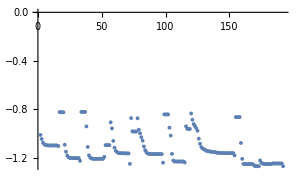

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 06:32:02 with grad NGAN

@cycle1:Tue 21 Feb 2023 06:36:28, fev:892, <E>: -1.2743428536263968 nansatz: 17 merged-smallθ-metric-bf-gmerged: {4, 1, 0, 14, 30}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 06:41:06, fev:1411, <E>: -1.2743428536263968 nansatz: 17 merged-smallθ-metric-bf-gmerged: {4, 1, 0, 14, 47}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 06:47:34, fev:2011, <E>: -1.2743428536263968 nansatz: 17 merged-smallθ-metric-bf-gmerged: {4, 1, 0, 14, 83}

dist 2.2 ; runtime 15.7942 min ; ϵ=0.135343

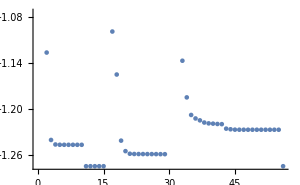

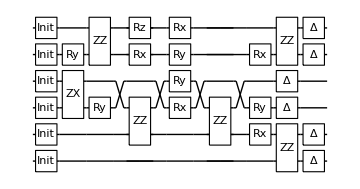

Compilation with automatically generated ansatz at Tue 21 Feb 2023 06:47:50 with grad NGAN

@cycle1:Tue 21 Feb 2023 06:51:41, fev:755, <E>: -0.9558923750118176 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 0, 16}

@cycle2:Tue 21 Feb 2023 06:58:12, fev:1808, <E>: -0.9731979224030285 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 25, 0, 44, 29}

@cycle3:Tue 21 Feb 2023 07:02:55, fev:2610, <E>: -0.8631929193573188 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 39, 0, 76, 50}

@cycle4:Tue 21 Feb 2023 07:08:29, fev:3436, <E>: -1.2283600227682971 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 91, 72}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 07:11:11, fev:3892, <E>: -1.2283600227682971 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 91, 84}

Slowing down @cycle 6

@cycle6:Tue 21 Feb 2023 07:14:48, fev:4449, <E>: -1.2283600227682971 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 91, 100}

dist 2.3 ; runtime 26.9667 min ; ϵ=0.178496

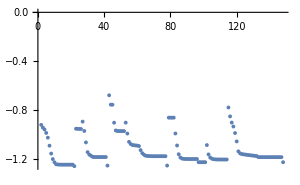

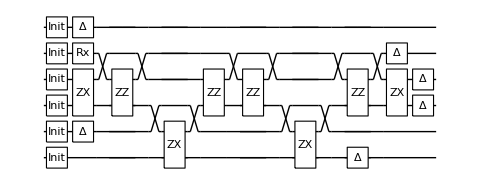

Compilation with automatically generated ansatz at Tue 21 Feb 2023 07:14:48 with grad NGAN

@cycle1:Tue 21 Feb 2023 07:18:24, fev:668, <E>: -1.2610504504507294 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 1, 32}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 07:23:07, fev:1137, <E>: -1.2610504504507294 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 1, 55}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 07:30:40, fev:1752, <E>: -1.2610504504507294 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 1, 87}

dist 2.4 ; runtime 16.357 min ; ϵ=0.143754

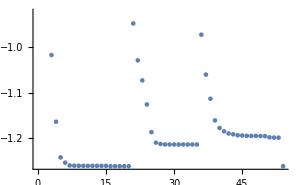

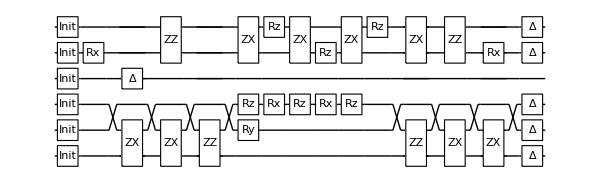

Compilation with automatically generated ansatz at Tue 21 Feb 2023 07:31:10 with grad NGAN

@cycle1:Tue 21 Feb 2023 07:35:16, fev:807, <E>: -1.2518131157991903 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 3, 38}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 07:39:50, fev:1266, <E>: -1.2518131157991903 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 3, 64}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 07:46:54, fev:1848, <E>: -1.2518131157991903 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 3, 94}

dist 2.5 ; runtime 16.3689 min ; ϵ=0.151514

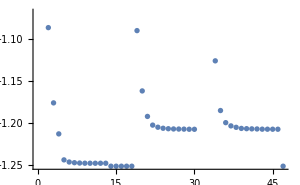

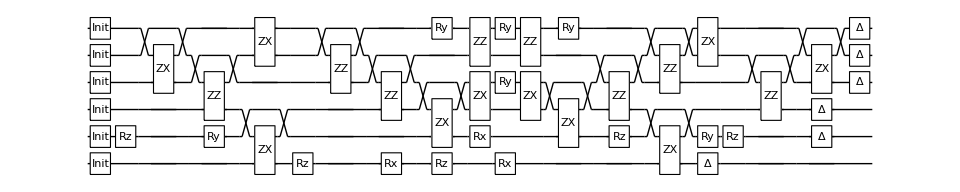

Compilation with automatically generated ansatz at Tue 21 Feb 2023 07:47:32 with grad NGAN

@cycle1:Tue 21 Feb 2023 07:52:02, fev:860, <E>: -0.902940050702576 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 25, 25}

@cycle2:Tue 21 Feb 2023 07:56:21, fev:1636, <E>: -1.0814443361234507 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 43, 49}

@cycle3:Tue 21 Feb 2023 08:00:25, fev:2406, <E>: -0.9033048164523925 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 39, 0, 69, 60}

@cycle4:Tue 21 Feb 2023 08:04:37, fev:3201, <E>: -0.9496366778535841 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 78, 79}

@cycle5:Tue 21 Feb 2023 08:11:15, fev:4219, <E>: -1.1975813440303793 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 102, 101}

@cycle6:Tue 21 Feb 2023 08:17:31, fev:5580, <E>: -1.2465605826417212 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 69, 0, 117, 114}

Slowing down @cycle 7

@cycle7:Tue 21 Feb 2023 08:20:33, fev:6011, <E>: -1.2465605826417212 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 69, 0, 117, 123}

Slowing down @cycle 8

@cycle8:Tue 21 Feb 2023 08:24:50, fev:6556, <E>: -1.2465605826417212 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 69, 0, 117, 137}

dist 2.75 ; runtime 37.751 min ; ϵ=0.154663

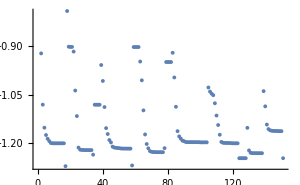

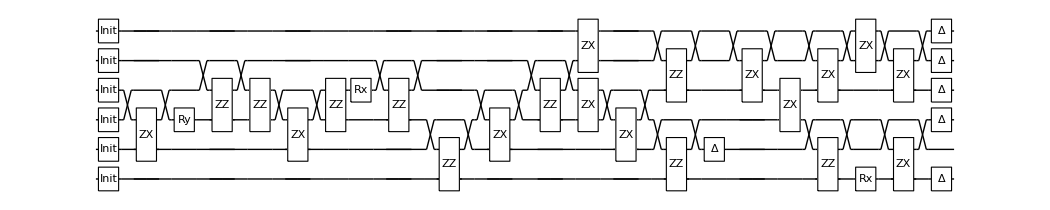

Compilation with automatically generated ansatz at Tue 21 Feb 2023 08:25:17 with grad NGAN

@cycle1:Tue 21 Feb 2023 08:28:56, fev:743, <E>: -0.9017489892866359 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 0, 26}

@cycle2:Tue 21 Feb 2023 08:35:18, fev:1800, <E>: -1.274711363785017 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 40, 39}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 08:37:32, fev:2244, <E>: -1.274711363785017 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 40, 54}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 08:40:50, fev:2815, <E>: -1.274711363785017 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 40, 72}

dist 3. ; runtime 15.5614 min ; ϵ=0.125623

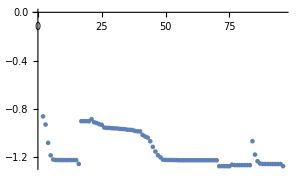

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 08:40:51 with grad NGAN

@cycle1:Tue 21 Feb 2023 08:44:38, fev:689, <E>: -1.2816903921641707 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 35}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 08:47:30, fev:1104, <E>: -1.2816903921641707 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 46}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 08:52:59, fev:1713, <E>: -1.2816903921641707 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 71}

dist 3.25 ; runtime 12.1897 min ; ϵ=0.118281

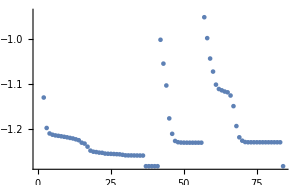

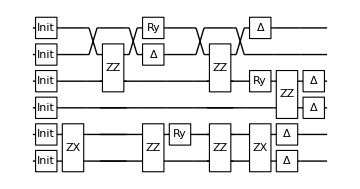

Compilation with automatically generated ansatz at Tue 21 Feb 2023 08:53:03 with grad NGAN

@cycle1:Tue 21 Feb 2023 08:57:17, fev:834, <E>: -1.25722569684351 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 15, 29}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 09:02:08, fev:1346, <E>: -1.25722569684351 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 15, 47}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 09:08:54, fev:1955, <E>: -1.25722569684351 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 15, 72}

dist 3.5 ; runtime 16.1117 min ; ϵ=0.142603

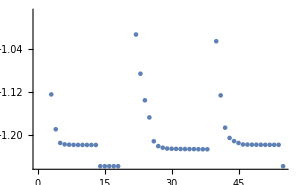

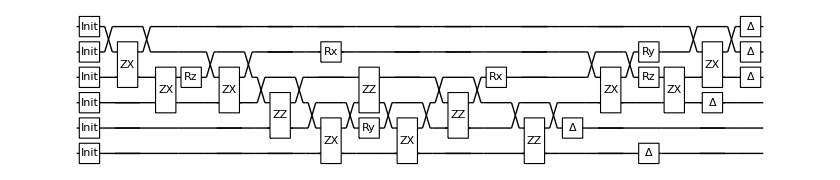

Compilation with automatically generated ansatz at Tue 21 Feb 2023 09:09:10 with grad NGAN

@cycle1:Tue 21 Feb 2023 09:13:14, fev:842, <E>: -1.2788530674704135 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 6, 23}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 09:16:58, fev:1289, <E>: -1.2788530674704135 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 6, 39}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 09:22:42, fev:1899, <E>: -1.2788530674704135 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 6, 54}

dist 3.75 ; runtime 13.7855 min ; ϵ=0.120922

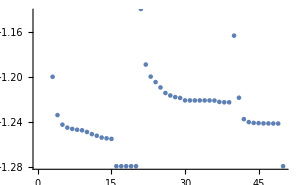

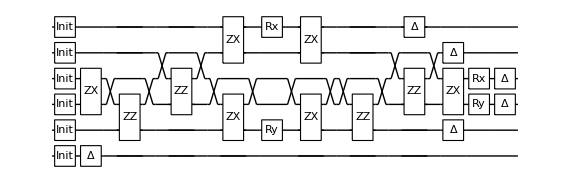

Compilation with automatically generated ansatz at Tue 21 Feb 2023 09:22:57 with grad NGAN

@cycle1:Tue 21 Feb 2023 09:27:35, fev:981, <E>: -1.274584128166886 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 28, 18}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 09:31:33, fev:1485, <E>: -1.274584128166886 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 28, 31}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 09:37:05, fev:2088, <E>: -1.274584128166886 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 28, 61}

dist 4. ; runtime 14.2677 min ; ϵ=0.125171

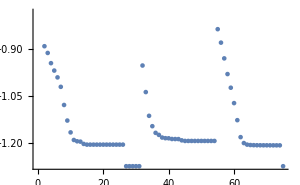

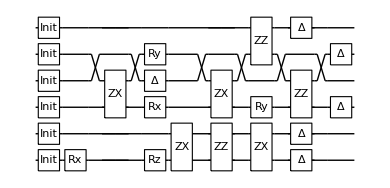

Compilation with automatically generated ansatz at Tue 21 Feb 2023 09:37:13 with grad NGAN

@cycle1:Tue 21 Feb 2023 09:43:46, fev:1136, <E>: -1.2433969416471713 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 6, 23}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 09:49:23, fev:1648, <E>: -1.2433969416471713 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 6, 37}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 09:57:35, fev:2254, <E>: -1.2433969416471713 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 6, 64}

dist 4.25 ; runtime 21.4933 min ; ϵ=0.156352

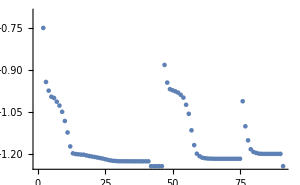

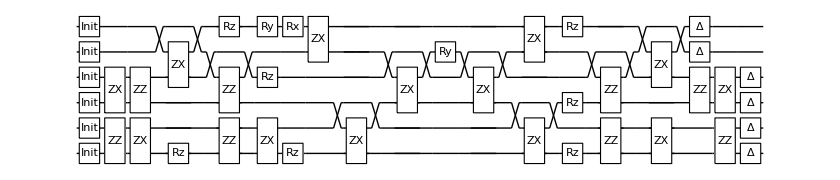

Compilation with automatically generated ansatz at Tue 21 Feb 2023 09:58:43 with grad NGAN

@cycle1:Tue 21 Feb 2023 10:02:55, fev:901, <E>: -1.2672892945985255 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 6, 17}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 10:06:43, fev:1342, <E>: -1.2672892945985255 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 6, 37}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 10:12:25, fev:1919, <E>: -1.2672892945985255 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 6, 56}

dist 4.5 ; runtime 13.9277 min ; ϵ=0.132457

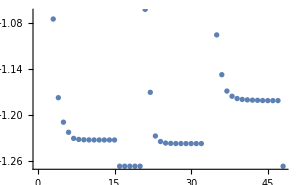

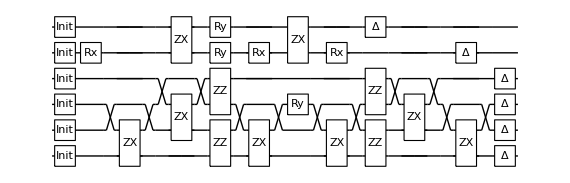

Compilation with automatically generated ansatz at Tue 21 Feb 2023 10:12:39 with grad NGAN

@cycle1:Tue 21 Feb 2023 10:16:37, fev:742, <E>: -1.2831596194978145 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 13, 48}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 10:20:56, fev:1229, <E>: -1.2831596194978145 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 13, 74}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 10:27:21, fev:1847, <E>: -1.2831596194978145 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 13, 94}

dist 4.75 ; runtime 14.8254 min ; ϵ=0.116586

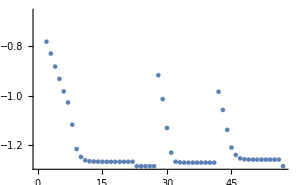

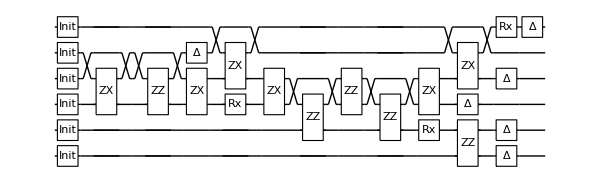

Compilation with automatically generated ansatz at Tue 21 Feb 2023 10:27:29 with grad NGAN

@cycle1:Tue 21 Feb 2023 10:31:52, fev:883, <E>: -1.265429513648601 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 12, 17}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 10:36:19, fev:1377, <E>: -1.265429513648601 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 12, 36}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 10:43:00, fev:2018, <E>: -1.265429513648601 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 12, 52}

dist 5. ; runtime 15.8051 min ; ϵ=0.134316

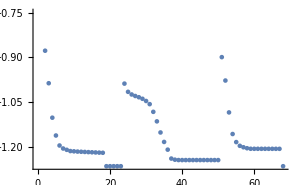

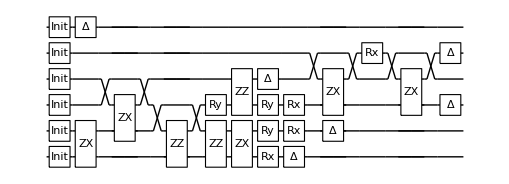

Compilation with automatically generated ansatz at Tue 21 Feb 2023 10:43:17 with grad NGAN

@cycle1:Tue 21 Feb 2023 10:47:50, fev:893, <E>: -1.279981404140812 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 19, 27}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 10:52:37, fev:1397, <E>: -1.279981404140812 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 19, 47}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 10:59:15, fev:1979, <E>: -1.279981404140812 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 19, 71}

dist 5.25 ; runtime 16.2199 min ; ϵ=0.119764

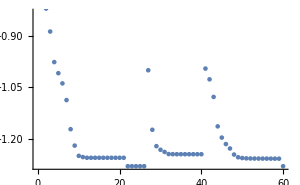

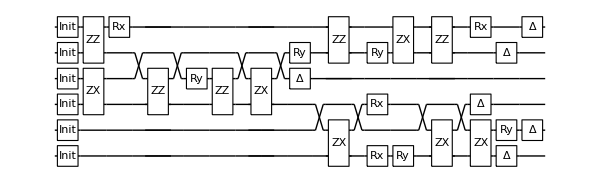

Compilation with automatically generated ansatz at Tue 21 Feb 2023 10:59:30 with grad NGAN

@cycle1:Tue 21 Feb 2023 11:02:51, fev:688, <E>: -0.9416586874206925 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 15, 26}

@cycle2:Tue 21 Feb 2023 11:07:54, fev:1583, <E>: -0.8761398843994994 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 40, 50}

@cycle3:Tue 21 Feb 2023 11:12:58, fev:2479, <E>: -1.2256756030796898 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 38, 0, 70, 78}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 11:15:32, fev:2895, <E>: -1.2256756030796898 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 38, 0, 70, 90}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 11:19:27, fev:3468, <E>: -1.2256756030796898 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 38, 0, 70, 108}

dist 5.5 ; runtime 20.0463 min ; ϵ=0.17407

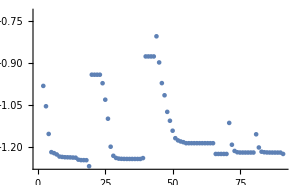

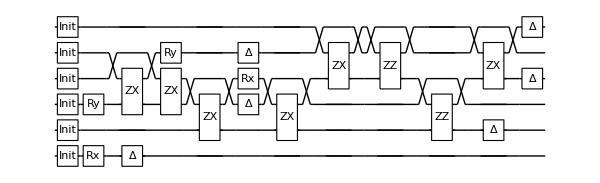

Compilation with automatically generated ansatz at Tue 21 Feb 2023 11:19:33 with grad NGAN

@cycle1:Tue 21 Feb 2023 11:23:12, fev:703, <E>: -1.2725585703759976 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 5, 22}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 11:27:47, fev:1184, <E>: -1.2725585703759976 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 5, 44}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 11:34:39, fev:1775, <E>: -1.2725585703759976 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 5, 68}

dist 5.75 ; runtime 15.732 min ; ϵ=0.127187

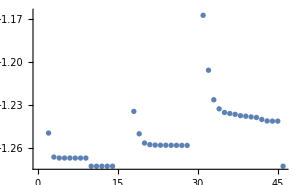

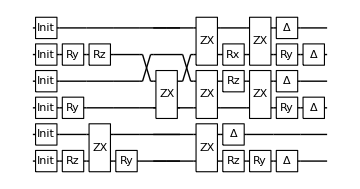

Compilation with automatically generated ansatz at Tue 21 Feb 2023 11:35:17 with grad NGAN

@cycle1:Tue 21 Feb 2023 11:41:28, fev:1048, <E>: -0.9933999962457439 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 0, 42}

@cycle2:Tue 21 Feb 2023 11:49:32, fev:1953, <E>: -0.8727719855657199 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 28, 66}

@cycle3:Tue 21 Feb 2023 11:56:34, fev:2940, <E>: -1.244177566699077 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 59, 99}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 11:59:28, fev:3378, <E>: -1.244177566699077 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 59, 113}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 12:03:49, fev:3951, <E>: -1.244177566699077 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 59, 126}

dist 6. ; runtime 28.6428 min ; ϵ=0.155568

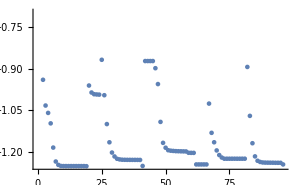

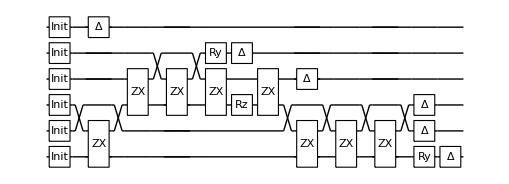

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### (1) Better expressibility: H3onSQC1.mx

```mathematica
H3onSQC1={};
```

Compilation with automatically generated ansatz at Tue 21 Feb 2023 13:34:48 with grad NGAN

@cycle1:Tue 21 Feb 2023 13:42:56, fev:1101, <E>: -0.5942394396169622 nansatz: 18 merged-smallθ-metric-bf-gmerged: {2, 15, 0, 8, 60}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 13:50:23, fev:1566, <E>: -0.5942394396169622 nansatz: 18 merged-smallθ-metric-bf-gmerged: {2, 15, 0, 8, 112}

@cycle3:Tue 21 Feb 2023 14:07:24, fev:2888, <E>: -0.5980685292498519 nansatz: 20 merged-smallθ-metric-bf-gmerged: {5, 54, 0, 21, 175}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 14:21:20, fev:3484, <E>: -0.5980685292498519 nansatz: 20 merged-smallθ-metric-bf-gmerged: {5, 54, 0, 21, 236}

Slowing down @cycle 5

@cycle5:Tue 21 Feb 2023 14:41:23, fev:4216, <E>: -0.5980685292498519 nansatz: 20 merged-smallθ-metric-bf-gmerged: {5, 54, 0, 21, 339}

dist 0.45 ; runtime 69.4914 min ; ϵ=0.396937

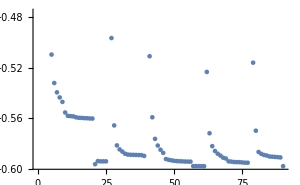

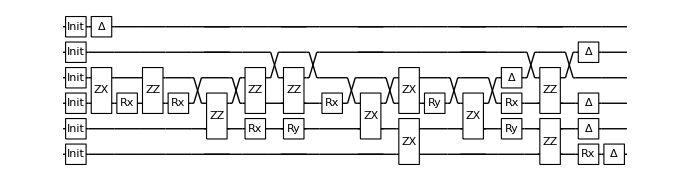

Compilation with automatically generated ansatz at Tue 21 Feb 2023 14:44:17 with grad NGAN

@cycle1:Tue 21 Feb 2023 14:51:02, fev:909, <E>: -0.8071756440053129 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 16, 46}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 14:57:04, fev:1385, <E>: -0.8071756440053129 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 16, 103}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 15:06:18, fev:1959, <E>: -0.8071756440053129 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 16, 150}

dist 0.5 ; runtime 22.2054 min ; ϵ=0.363357

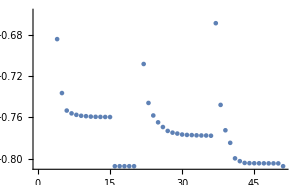

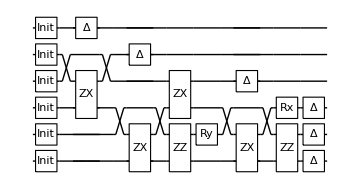

Compilation with automatically generated ansatz at Tue 21 Feb 2023 15:06:30 with grad NGAN

@cycle1:Tue 21 Feb 2023 15:13:14, fev:840, <E>: -0.9603639472376304 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 22, 0, 8, 38}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 15:19:39, fev:1296, <E>: -0.9603639472376304 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 22, 0, 8, 87}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 15:30:00, fev:1872, <E>: -0.9603639472376304 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 22, 0, 8, 130}

dist 0.55 ; runtime 23.7399 min ; ϵ=0.336634

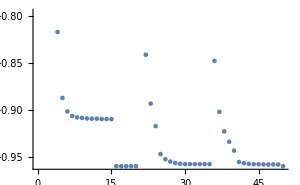

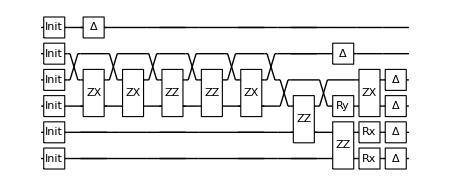

Compilation with automatically generated ansatz at Tue 21 Feb 2023 15:30:14 with grad NGAN

@cycle1:Tue 21 Feb 2023 15:37:38, fev:933, <E>: -1.0765750706679438 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 9, 2, 24, 50}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 15:43:10, fev:1381, <E>: -1.0765750706679438 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 9, 2, 24, 107}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 15:52:20, fev:1951, <E>: -1.0765750706679438 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 9, 2, 24, 164}

dist 0.6 ; runtime 22.2394 min ; ϵ=0.31174

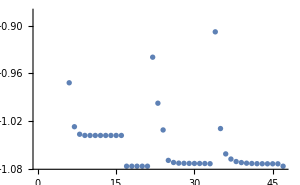

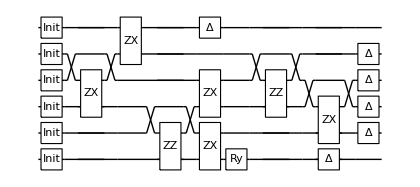

Compilation with automatically generated ansatz at Tue 21 Feb 2023 15:52:29 with grad NGAN

@cycle1:Tue 21 Feb 2023 15:59:14, fev:885, <E>: -1.1604782360687702 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 9, 8, 12, 62}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 16:06:11, fev:1339, <E>: -1.1604782360687702 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 9, 8, 12, 113}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 16:17:15, fev:1908, <E>: -1.1604782360687702 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 9, 8, 12, 176}

dist 0.65 ; runtime 25.0875 min ; ϵ=0.293311

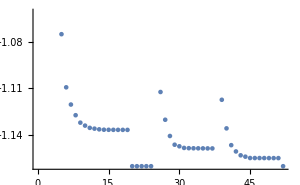

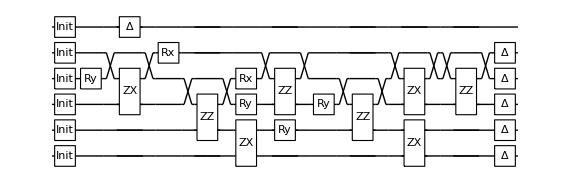

Compilation with automatically generated ansatz at Tue 21 Feb 2023 16:17:34 with grad NGAN

@cycle1:Tue 21 Feb 2023 16:24:51, fev:903, <E>: -1.2225258480843357 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 15, 7, 11, 51}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 16:31:15, fev:1339, <E>: -1.2225258480843357 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 15, 7, 11, 103}

$Aborted

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H3onSQC1, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H3onSQC1.mx", H3onSQC1];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH3}]
```

### (2) Better expressibility+perfect init+perfect meas: H3onSQC2.mx

```mathematica
H3onSQC2={};
```

Compilation with automatically generated ansatz at Tue 21 Feb 2023 16:32:34 with grad NGAN

@cycle1:Tue 21 Feb 2023 16:41:25, fev:1042, <E>: -0.9686530516423527 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 18, 61}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 16:49:05, fev:1503, <E>: -0.9686530516423527 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 18, 114}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 17:00:41, fev:2083, <E>: -0.9686530516423527 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 18, 160}

dist 0.45 ; runtime 28.5371 min ; ϵ=0.0263527

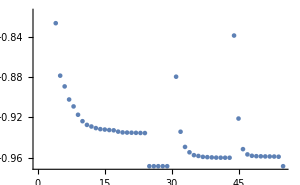

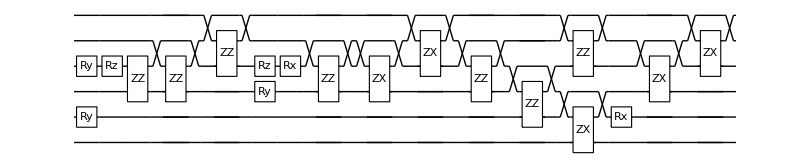

Compilation with automatically generated ansatz at Tue 21 Feb 2023 17:01:06 with grad NGAN

@cycle1:Tue 21 Feb 2023 17:09:30, fev:1208, <E>: -1.1445415487303459 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 4, 55}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 17:19:06, fev:1701, <E>: -1.1445415487303459 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 4, 108}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 17:32:49, fev:2308, <E>: -1.1445415487303459 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 4, 187}

dist 0.5 ; runtime 33.1836 min ; ϵ=0.0259909

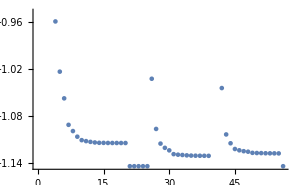

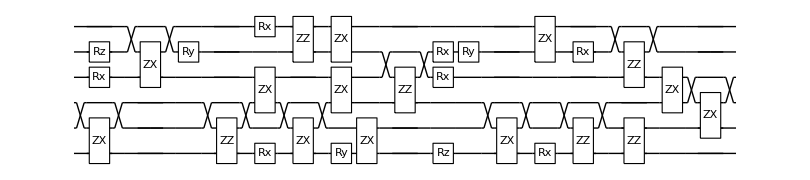

Compilation with automatically generated ansatz at Tue 21 Feb 2023 17:34:17 with grad NGAN

@cycle1:Tue 21 Feb 2023 17:42:00, fev:1018, <E>: -1.278914148488367 nansatz: 26 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 12, 37}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 17:49:28, fev:1486, <E>: -1.278914148488367 nansatz: 26 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 12, 90}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 18:02:10, fev:2056, <E>: -1.278914148488367 nansatz: 26 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 12, 158}

dist 0.55 ; runtime 28.5869 min ; ϵ=0.0180835

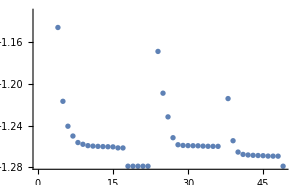

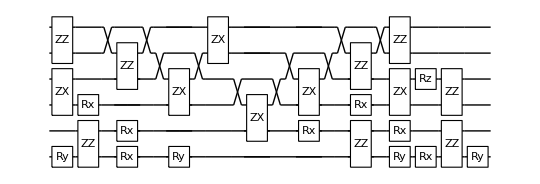

Compilation with automatically generated ansatz at Tue 21 Feb 2023 18:02:53 with grad NGAN

@cycle1:Tue 21 Feb 2023 18:09:52, fev:1019, <E>: -1.3697069956770154 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 8, 0, 19, 52}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 18:16:27, fev:1479, <E>: -1.3697069956770154 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 8, 0, 19, 95}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 18:27:17, fev:2060, <E>: -1.3697069956770154 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 8, 0, 19, 160}

dist 0.6 ; runtime 24.7553 min ; ϵ=0.018608

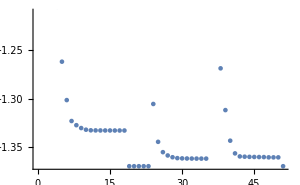

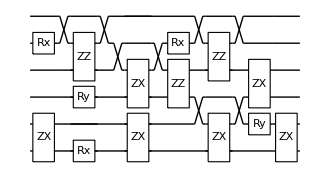

Compilation with automatically generated ansatz at Tue 21 Feb 2023 18:27:38 with grad NGAN

@cycle1:Tue 21 Feb 2023 18:35:07, fev:989, <E>: -1.4307563179144647 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 14, 52}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 18:43:14, fev:1451, <E>: -1.4307563179144647 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 14, 89}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 18:54:43, fev:2024, <E>: -1.4307563179144647 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 14, 152}

dist 0.65 ; runtime 27.5441 min ; ϵ=0.0230326

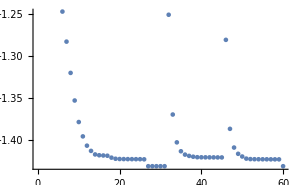

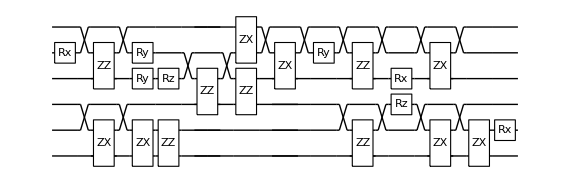

Compilation with automatically generated ansatz at Tue 21 Feb 2023 18:55:11 with grad NGAN

@cycle1:Tue 21 Feb 2023 19:02:02, fev:821, <E>: -1.4748771492976513 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 13, 52}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 19:09:08, fev:1291, <E>: -1.4748771492976513 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 13, 97}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 19:20:13, fev:1867, <E>: -1.4748771492976513 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 13, 174}

dist 0.7 ; runtime 25.3956 min ; ϵ=0.0250599

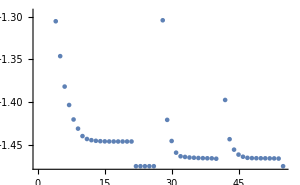

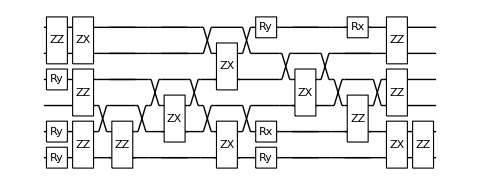

Compilation with automatically generated ansatz at Tue 21 Feb 2023 19:20:35 with grad NGAN

@cycle1:Tue 21 Feb 2023 19:27:35, fev:1020, <E>: -1.503837151104396 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 3, 1, 7, 62}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 19:36:46, fev:1476, <E>: -1.503837151104396 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 3, 1, 7, 112}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 19:50:05, fev:2042, <E>: -1.503837151104396 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 3, 1, 7, 188}

dist 0.75 ; runtime 30.4492 min ; ϵ=0.0276672

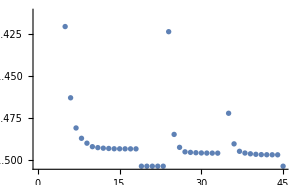

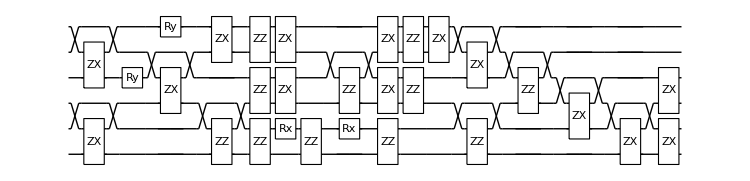

Compilation with automatically generated ansatz at Tue 21 Feb 2023 19:51:02 with grad NGAN

@cycle1:Tue 21 Feb 2023 19:58:01, fev:844, <E>: -1.5211821715925056 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 13, 44}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 20:05:17, fev:1292, <E>: -1.5211821715925056 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 13, 112}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 20:18:02, fev:1856, <E>: -1.5211821715925056 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 13, 176}

dist 0.8 ; runtime 27.5544 min ; ϵ=0.0308464

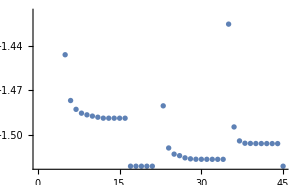

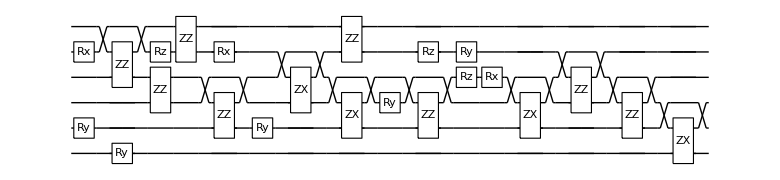

Compilation with automatically generated ansatz at Tue 21 Feb 2023 20:18:35 with grad NGAN

@cycle1:Tue 21 Feb 2023 20:25:06, fev:833, <E>: -1.5307099461618419 nansatz: 10 merged-smallθ-metric-bf-gmerged: {3, 21, 0, 8, 47}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 20:31:10, fev:1269, <E>: -1.5307099461618419 nansatz: 10 merged-smallθ-metric-bf-gmerged: {3, 21, 0, 8, 94}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 20:41:14, fev:1837, <E>: -1.5307099461618419 nansatz: 10 merged-smallθ-metric-bf-gmerged: {3, 21, 0, 8, 165}

dist 0.85 ; runtime 22.7933 min ; ϵ=0.0334688

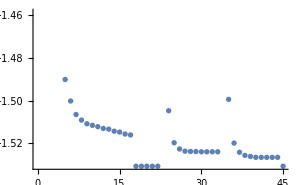

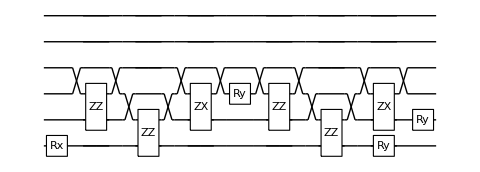

Compilation with automatically generated ansatz at Tue 21 Feb 2023 20:41:23 with grad NGAN

@cycle1:Tue 21 Feb 2023 20:49:19, fev:1054, <E>: -1.5294741101333487 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 10, 58}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 20:57:14, fev:1503, <E>: -1.5294741101333487 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 10, 91}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 21:10:08, fev:2063, <E>: -1.5294741101333487 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 10, 161}

dist 0.9 ; runtime 29.5486 min ; ϵ=0.0405056

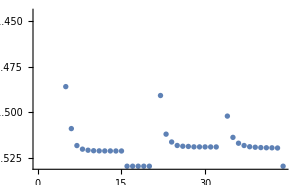

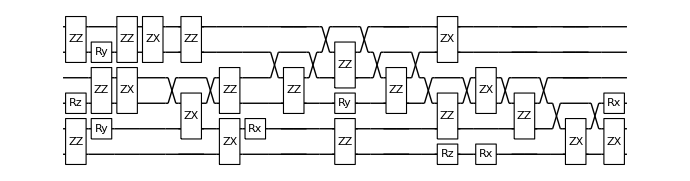

Compilation with automatically generated ansatz at Tue 21 Feb 2023 21:10:56 with grad NGAN

@cycle1:Tue 21 Feb 2023 21:18:10, fev:984, <E>: -1.5243605646665126 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 9, 50}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 21:25:53, fev:1425, <E>: -1.5243605646665126 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 9, 110}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 21:39:01, fev:2026, <E>: -1.5243605646665126 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 9, 172}

dist 0.95 ; runtime 28.6236 min ; ϵ=0.0466148

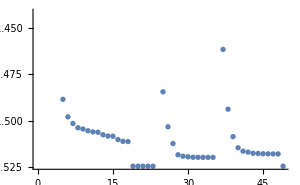

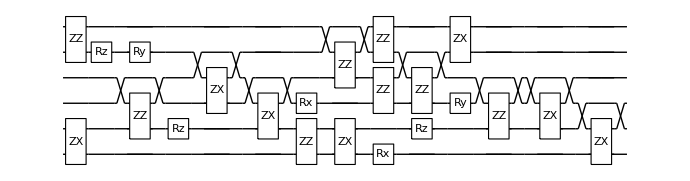

Compilation with automatically generated ansatz at Tue 21 Feb 2023 21:39:34 with grad NGAN

@cycle1:Tue 21 Feb 2023 21:47:07, fev:958, <E>: -1.5229226423699165 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 18, 52}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 21:54:27, fev:1397, <E>: -1.5229226423699165 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 18, 112}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 22:05:46, fev:1949, <E>: -1.5229226423699165 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 18, 179}

dist 1. ; runtime 26.7182 min ; ϵ=0.0454292

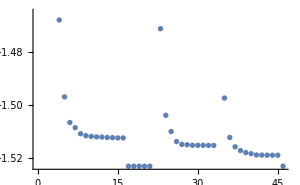

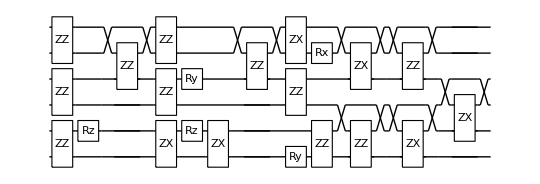

Compilation with automatically generated ansatz at Tue 21 Feb 2023 22:06:17 with grad NGAN

@cycle1:Tue 21 Feb 2023 22:12:43, fev:970, <E>: -1.513718237885655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 22, 46}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 22:18:57, fev:1397, <E>: -1.513718237885655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 22, 100}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 22:27:49, fev:1937, <E>: -1.513718237885655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 22, 170}

dist 1.05 ; runtime 21.7621 min ; ϵ=0.0493124

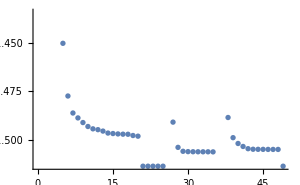

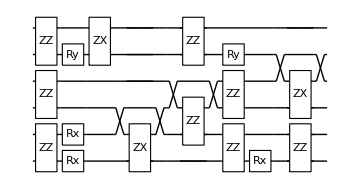

Compilation with automatically generated ansatz at Tue 21 Feb 2023 22:28:03 with grad NGAN

@cycle1:Tue 21 Feb 2023 22:34:49, fev:1023, <E>: -1.5010918932893944 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 10, 7, 12, 60}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 22:40:29, fev:1457, <E>: -1.5010918932893944 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 10, 7, 12, 96}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 22:49:42, fev:2000, <E>: -1.5010918932893944 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 10, 7, 12, 153}

dist 1.1 ; runtime 21.9768 min ; ϵ=0.0546455

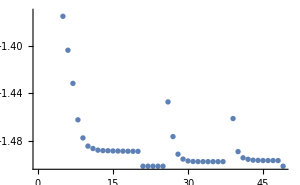

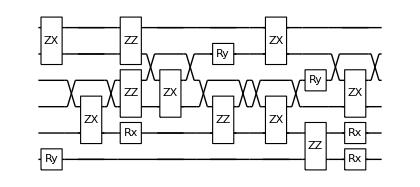

Compilation with automatically generated ansatz at Tue 21 Feb 2023 22:50:01 with grad NGAN

@cycle1:Tue 21 Feb 2023 22:56:29, fev:959, <E>: -1.487227633778578 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 12, 60}

@cycle2:Tue 21 Feb 2023 23:05:34, fev:1881, <E>: -1.51173230310539 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 51, 0, 24, 100}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 23:10:12, fev:2313, <E>: -1.51173230310539 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 51, 0, 24, 128}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 23:17:35, fev:2862, <E>: -1.51173230310539 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 51, 0, 24, 178}

dist 1.15 ; runtime 27.961 min ; ϵ=0.035319

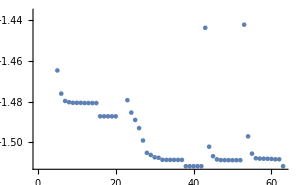

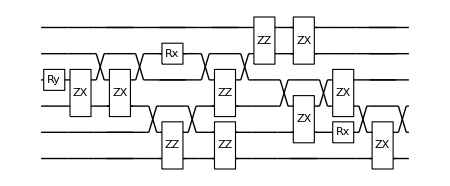

Compilation with automatically generated ansatz at Tue 21 Feb 2023 23:17:59 with grad NGAN

@cycle1:Tue 21 Feb 2023 23:24:44, fev:863, <E>: -1.4711544296566361 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 12, 50}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 23:31:50, fev:1304, <E>: -1.4711544296566361 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 12, 95}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 23:42:31, fev:1853, <E>: -1.4711544296566361 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 12, 164}

dist 1.2 ; runtime 25.2664 min ; ϵ=0.0662857

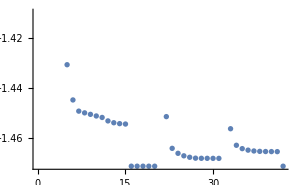

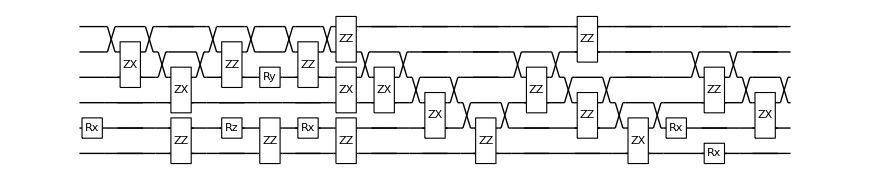

Compilation with automatically generated ansatz at Tue 21 Feb 2023 23:43:15 with grad NGAN

@cycle1:Tue 21 Feb 2023 23:49:44, fev:785, <E>: -1.4553357825160935 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 12, 4, 20, 59}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 23:55:11, fev:1245, <E>: -1.4553357825160935 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 12, 4, 20, 94}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:04:44, fev:1837, <E>: -1.4553357825160935 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 12, 4, 20, 152}

dist 1.25 ; runtime 21.5906 min ; ϵ=0.0719483

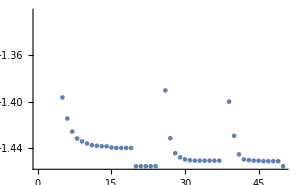

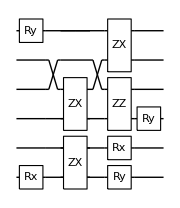

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:04:51 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:11:29, fev:980, <E>: -1.4370999704570577 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 12, 43}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:20:20, fev:1426, <E>: -1.4370999704570577 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 12, 105}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:33:06, fev:1993, <E>: -1.4370999704570577 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 12, 173}

dist 1.3 ; runtime 28.9111 min ; ϵ=0.0797927

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:33:46 with grad NGAN

@cycle1:Wed 22 Feb 2023 00:41:44, fev:1191, <E>: -1.42032490729001 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 20, 49}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 00:48:49, fev:1638, <E>: -1.42032490729001 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 20, 106}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 00:59:29, fev:2196, <E>: -1.42032490729001 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 20, 173}

dist 1.35 ; runtime 26.0762 min ; ϵ=0.0861916

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 00:59:51 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:06:58, fev:997, <E>: -1.4004909131953216 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 20, 59}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:14:28, fev:1436, <E>: -1.4004909131953216 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 20, 110}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:26:24, fev:1988, <E>: -1.4004909131953216 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 20, 188}

dist 1.4 ; runtime 27.0697 min ; ϵ=0.095865

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:26:55 with grad NGAN

@cycle1:Wed 22 Feb 2023 01:34:03, fev:1020, <E>: -1.4244695969729628 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 6, 3, 13, 56}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 01:41:50, fev:1468, <E>: -1.4244695969729628 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 6, 3, 13, 103}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 01:53:34, fev:2032, <E>: -1.4244695969729628 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 6, 3, 13, 169}

dist 1.45 ; runtime 27.4321 min ; ϵ=0.0620983

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 01:54:21 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:01:33, fev:977, <E>: -1.366674808824185 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 18, 42}

@cycle2:Wed 22 Feb 2023 02:13:32, fev:2056, <E>: -1.403696545740542 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 54, 0, 25, 91}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:18:38, fev:2483, <E>: -1.403696545740542 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 54, 0, 25, 147}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 02:26:16, fev:3030, <E>: -1.403696545740542 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 54, 0, 25, 198}

dist 1.5 ; runtime 32.3352 min ; ϵ=0.0735751

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:26:41 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:34:19, fev:1058, <E>: -1.393339807431528 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 28, 49}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 02:40:07, fev:1504, <E>: -1.393339807431528 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 28, 91}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 02:49:22, fev:2068, <E>: -1.393339807431528 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 28, 166}

dist 1.6 ; runtime 22.9711 min ; ϵ=0.0671288

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 02:49:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 02:57:31, fev:1091, <E>: -1.3514713867744914 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 19, 49}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 03:05:08, fev:1523, <E>: -1.3514713867744914 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 19, 102}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 03:16:21, fev:2073, <E>: -1.3514713867744914 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 19, 149}

dist 1.7 ; runtime 27.1859 min ; ϵ=0.0948354

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 03:16:51 with grad NGAN

@cycle1:Wed 22 Feb 2023 03:24:35, fev:984, <E>: -1.3621572679546656 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 10, 3, 5, 47}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 03:32:43, fev:1420, <E>: -1.3621572679546656 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 10, 3, 5, 98}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 03:46:13, fev:1974, <E>: -1.3621572679546656 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 10, 3, 5, 167}

dist 1.8 ; runtime 30.2333 min ; ϵ=0.072645

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 03:47:05 with grad NGAN

@cycle1:Wed 22 Feb 2023 03:53:30, fev:906, <E>: -1.370560234881224 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 4, 7, 15, 57}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 03:59:44, fev:1333, <E>: -1.370560234881224 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 4, 7, 15, 119}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 04:09:55, fev:1914, <E>: -1.370560234881224 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 4, 7, 15, 183}

dist 1.9 ; runtime 23.2851 min ; ϵ=0.0551113

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 04:10:22 with grad NGAN

@cycle1:Wed 22 Feb 2023 04:16:27, fev:819, <E>: -1.3779582319551265 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 6, 0, 21, 65}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 04:22:37, fev:1237, <E>: -1.3779582319551265 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 6, 0, 21, 114}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 04:32:58, fev:1799, <E>: -1.3779582319551265 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 6, 0, 21, 171}

dist 2. ; runtime 22.8465 min ; ϵ=0.0408286

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 04:33:13 with grad NGAN

@cycle1:Wed 22 Feb 2023 04:40:39, fev:1052, <E>: -1.3870974836784462 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 21, 42}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 04:47:21, fev:1476, <E>: -1.3870974836784462 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 21, 94}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 04:58:51, fev:2023, <E>: -1.3870974836784462 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 21, 151}

dist 2.1 ; runtime 26.0547 min ; ϵ=0.0264593

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 04:59:17 with grad NGAN

@cycle1:Wed 22 Feb 2023 05:06:01, fev:865, <E>: -1.3877070094188055 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 3, 58}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 05:15:06, fev:1304, <E>: -1.3877070094188055 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 3, 106}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 05:29:08, fev:1857, <E>: -1.3877070094188055 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 3, 177}

dist 2.2 ; runtime 31.229 min ; ϵ=0.0219792

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 05:30:30 with grad NGAN

@cycle1:Wed 22 Feb 2023 05:36:57, fev:818, <E>: -1.3909971934352474 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 13, 58}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 05:42:59, fev:1231, <E>: -1.3909971934352474 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 13, 103}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 05:52:46, fev:1775, <E>: -1.3909971934352474 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 13, 186}

dist 2.3 ; runtime 22.5746 min ; ϵ=0.0158585

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 05:53:05 with grad NGAN

@cycle1:Wed 22 Feb 2023 06:00:36, fev:885, <E>: -1.3947039458808124 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 12, 10, 11, 40}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 06:06:24, fev:1304, <E>: -1.3947039458808124 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 12, 10, 11, 92}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 06:16:17, fev:1874, <E>: -1.3947039458808124 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 12, 10, 11, 150}

dist 2.4 ; runtime 23.397 min ; ϵ=0.0101001

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 06:16:29 with grad NGAN

@cycle1:Wed 22 Feb 2023 06:24:04, fev:962, <E>: -1.3959113393869902 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 10, 39}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 06:30:54, fev:1390, <E>: -1.3959113393869902 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 10, 91}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 06:42:12, fev:1939, <E>: -1.3959113393869902 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 10, 146}

dist 2.5 ; runtime 26.1778 min ; ϵ=0.00741549

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 06:42:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 06:49:58, fev:1016, <E>: -1.3981477529806035 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 23, 50}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 06:56:33, fev:1433, <E>: -1.3981477529806035 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 23, 99}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 07:07:02, fev:1973, <E>: -1.3981477529806035 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 23, 167}

dist 2.75 ; runtime 24.776 min ; ϵ=0.00307552

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 07:07:27 with grad NGAN

@cycle1:Wed 22 Feb 2023 07:14:32, fev:933, <E>: -1.3979806729478095 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 30, 42}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 07:20:52, fev:1360, <E>: -1.3979806729478095 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 30, 96}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 07:30:49, fev:1909, <E>: -1.3979806729478095 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 30, 153}

dist 3. ; runtime 23.5506 min ; ϵ=0.00235367

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 07:31:00 with grad NGAN

@cycle1:Wed 22 Feb 2023 07:37:37, fev:879, <E>: -1.3991755982937712 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 8, 54}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 07:44:06, fev:1285, <E>: -1.3991755982937712 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 8, 82}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 07:55:11, fev:1837, <E>: -1.3991755982937712 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 8, 143}

dist 3.25 ; runtime 24.5735 min ; ϵ=0.000795572

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 07:55:34 with grad NGAN

@cycle1:Wed 22 Feb 2023 08:01:44, fev:814, <E>: -1.3949124181142352 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 7, 61}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 08:09:33, fev:1244, <E>: -1.3949124181142352 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 7, 103}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 08:21:16, fev:1775, <E>: -1.3949124181142352 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 7, 160}

dist 3.5 ; runtime 26.4268 min ; ϵ=0.00491623

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 08:22:00 with grad NGAN

@cycle1:Wed 22 Feb 2023 08:28:44, fev:755, <E>: -1.3991279779530925 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 7, 54}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 08:34:58, fev:1169, <E>: -1.3991279779530925 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 7, 113}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 08:45:02, fev:1705, <E>: -1.3991279779530925 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 7, 175}

dist 3.75 ; runtime 23.2749 min ; ϵ=0.000647032

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 08:45:17 with grad NGAN

@cycle1:Wed 22 Feb 2023 08:51:37, fev:911, <E>: -1.399457695268489 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 6, 53}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 08:58:03, fev:1335, <E>: -1.399457695268489 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 6, 110}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 09:08:44, fev:1882, <E>: -1.399457695268489 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 6, 193}

dist 4. ; runtime 23.8599 min ; ϵ=0.000297911

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:09:08 with grad NGAN

@cycle1:Wed 22 Feb 2023 09:16:26, fev:966, <E>: -1.3991587109421921 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 10, 59}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 09:23:08, fev:1389, <E>: -1.3991587109421921 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 10, 119}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 09:34:31, fev:1938, <E>: -1.3991587109421921 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 10, 198}

dist 4.25 ; runtime 26.0266 min ; ϵ=0.000590137

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:35:10 with grad NGAN

@cycle1:Wed 22 Feb 2023 09:41:32, fev:765, <E>: -1.3997441630064622 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 13, 10, 13, 39}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 09:46:08, fev:1182, <E>: -1.3997441630064622 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 13, 10, 13, 76}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 09:54:12, fev:1740, <E>: -1.3997441630064622 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 13, 10, 13, 152}

dist 4.5 ; runtime 19.051 min ; ϵ=2.41868×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 09:54:13 with grad NGAN

@cycle1:Wed 22 Feb 2023 10:02:13, fev:1097, <E>: -1.3962858970464609 nansatz: 10 merged-smallθ-metric-bf-gmerged: {5, 12, 0, 14, 57}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 10:08:15, fev:1534, <E>: -1.3962858970464609 nansatz: 10 merged-smallθ-metric-bf-gmerged: {5, 12, 0, 14, 97}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 10:17:44, fev:2076, <E>: -1.3962858970464609 nansatz: 10 merged-smallθ-metric-bf-gmerged: {5, 12, 0, 14, 154}

dist 4.75 ; runtime 23.818 min ; ϵ=0.000103124

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 10:18:03 with grad NGAN

@cycle1:Wed 22 Feb 2023 10:25:05, fev:874, <E>: -1.3908381537456358 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 0, 62}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 10:34:28, fev:1309, <E>: -1.3908381537456358 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 0, 122}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 10:49:34, fev:1866, <E>: -1.3908381537456358 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 0, 194}

dist 5. ; runtime 33.1087 min ; ϵ=0.00047306

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 10:51:09 with grad NGAN

@cycle1:Wed 22 Feb 2023 10:58:22, fev:937, <E>: -1.399336313921274 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 20, 50}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 11:06:23, fev:1367, <E>: -1.399336313921274 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 20, 87}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 11:16:58, fev:1922, <E>: -1.399336313921274 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 20, 171}

dist 5.25 ; runtime 26.4196 min ; ϵ=0.000409285

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 11:17:35 with grad NGAN

@cycle1:Wed 22 Feb 2023 11:24:30, fev:1115, <E>: -1.3971911798030943 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 10, 44}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 11:31:14, fev:1523, <E>: -1.3971911798030943 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 10, 75}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 11:42:55, fev:2057, <E>: -1.3971911798030943 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 10, 127}

dist 5.5 ; runtime 26.0922 min ; ϵ=0.00255438

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 11:43:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 11:50:38, fev:1054, <E>: -1.3991673151722377 nansatz: 23 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 7, 54}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 11:57:20, fev:1474, <E>: -1.3991673151722377 nansatz: 23 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 7, 116}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:08:08, fev:2006, <E>: -1.3991673151722377 nansatz: 23 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 7, 178}

dist 5.75 ; runtime 24.9933 min ; ϵ=0.00057827

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 12:08:40 with grad NGAN

@cycle1:Wed 22 Feb 2023 12:15:44, fev:1044, <E>: -1.3920663450566184 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 17, 35}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 12:22:12, fev:1452, <E>: -1.3920663450566184 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 17, 80}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 12:32:53, fev:1994, <E>: -1.3920663450566184 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 17, 164}

dist 6. ; runtime 24.6783 min ; ϵ=0.0076792

-Graphics-

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
conf["initcirc"]={};
conf["virtualmeas"]={};
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H3onSQC2, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H3onSQC2.mx", H3onSQC2];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH3}]
```

### (2) Better expressibility+perfect : H3onSQC3.mx

```mathematica
Options@SuperconductingHub
```

{qubitsNum→6,T1→<|0→63,1→93,2→109,3→115,4→68,5→125|>,T2→<|0→113,1→149,2→185,3→161,4→122,5→200|>,ExcitedInit→<|0→0.032,1→0.021,2→0.008,3→0.009,4→0.025,5→0.007|>,QubitFreq→<|0→4500,1→4900,2→4700,3→5100,4→4900,5→5300|>,ExchangeCoupling→<|0<->1→4,0<->2→1.5,1<->3→1.5,2<->3→4,2<->4→1.5,3<->5→1.5,4<->5→4|>,Anharmonicity→<|0→296.7,1→298.6,2→297.4,3→298.3,4→297.2,5→299.1|>,FidRead→<|0→0.9,1→0.92,2→0.96,3→0.97,4→0.93,5→0.97|>,DurMeas→5,DurRxRy→0.05,DurZX→0.5,DurZZ→0.5,StdPassiveNoise→True,ZZPassiveNoise→True}

```mathematica
H3onSQC3={};
```

```mathematica
Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[StdPassiveNoise->False,ZZPassiveNoise->False];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
conf["initcirc"]={};
conf["virtualmeas"]={};
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H3onSQC3, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H3onSQC3.mx", H3onSQC3];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH3}]
```

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:30:16 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:34:22, fev:990, <E>: -0.9845420880165972 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 4, 59}

@cycle2:Wed 22 Feb 2023 14:41:27, fev:2129, <E>: -0.9847024443075487 nansatz: 30 merged-smallθ-metric-bf-gmerged: {5, 32, 0, 19, 108}

Slowing down @cycle 3

@cycle3:Wed 22 Feb 2023 14:45:28, fev:2565, <E>: -0.9847024443075487 nansatz: 30 merged-smallθ-metric-bf-gmerged: {5, 32, 0, 19, 157}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 14:51:26, fev:3130, <E>: -0.9847024443075487 nansatz: 30 merged-smallθ-metric-bf-gmerged: {5, 32, 0, 19, 215}

dist 0.45 ; runtime 24.154 min ; ϵ=0.0103033

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 14:54:25 with grad NGAN

@cycle1:Wed 22 Feb 2023 14:58:58, fev:1064, <E>: -1.1570221769118358 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 6, 53}

@cycle2:Wed 22 Feb 2023 15:05:16, fev:2115, <E>: -1.158136368869278 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 47, 0, 22, 103}

@cycle3:Wed 22 Feb 2023 15:10:30, fev:3141, <E>: -1.158663827211898 nansatz: 27 merged-smallθ-metric-bf-gmerged: {3, 76, 0, 28, 144}

Slowing down @cycle 4

@cycle4:Wed 22 Feb 2023 15:13:53, fev:3582, <E>: -1.158663827211898 nansatz: 27 merged-smallθ-metric-bf-gmerged: {3, 76, 0, 28, 192}

Slowing down @cycle 5

@cycle5:Wed 22 Feb 2023 15:18:52, fev:4137, <E>: -1.158663827211898 nansatz: 27 merged-smallθ-metric-bf-gmerged: {3, 76, 0, 28, 251}

dist 0.5 ; runtime 25.2641 min ; ϵ=0.0118686

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Wed 22 Feb 2023 15:19:41 with grad NGAN

@cycle1:Wed 22 Feb 2023 15:23:40, fev:988, <E>: -1.2814215662188917 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 5, 47}

Slowing down @cycle 2

@cycle2:Wed 22 Feb 2023 15:27:07, fev:1427, <E>: -1.2814215662188917 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 5, 97}

@cycle3:Wed 22 Feb 2023 15:35:12, fev:2765, <E>: -1.2829235538673365 nansatz: 20 merged-smallθ-metric-bf-gmerged: {4, 53, 0, 18, 170}

$Aborted